## Two kings and a white rook

```mathematica
n=3;(*size of the board*)
```

```mathematica
kingMoves[x_,y_]:=Module[{ans={}},
If[x>1,
AppendTo[ans,{x-1,y}];
If[y>1,AppendTo[ans,{x-1,y-1}]];
If[y<n,AppendTo[ans,{x-1,y+1}]];
];
If[x<n,
AppendTo[ans,{x+1,y}];
If[y>1,AppendTo[ans,{x+1,y-1}]];
If[y<n,AppendTo[ans,{x+1,y+1}]];
];
If[y>1,AppendTo[ans,{x,y-1}]];
If[y<n,AppendTo[ans,{x,y+1}]];
ans
];(*returns a list of valid moves for a single king*)
```

```mathematica
rookMoves[x_,y_]:=DeleteCases[Join[{#,y}&/@Range[n],{x,#}&/@Range[n]],{x,y}];(*returns a list of valid moves for a single rook*)
```

```mathematica
validPosition[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_}]:=(!(Abs[w1-b1]<=1&&Abs[w2-b2]<=1))&&(!(w1==r1&&w2==r2))&&(!(b1==r1&&b2==r2))&&(!(m==1&&(r1==b1&&(w1!=b1||w2<Min[b2,r2]||w2>Max[b2,r2]))))&&(!(m==1&&(r2==b2&&(w2!=b2||w1<Min[b1,r1]||w1>Max[b1,r1]))));
(*{{white king x, white king y}, {black king x, black king y}, 1->white's move; 0->black's move}*)
```

```mathematica
nextPositions[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_}]:=Module[{ans={}},
If[m==1,(*white's move*)
ans=Join[{#,{b1,b2},{r1,r2},0}&/@kingMoves[w1,w2],{{w1,w2},{b1,b2},#,0}&/@rookMoves[r1,r2]]
];
If[m==0,(*black's move*)
ans={{w1,w2},#,{r1,r2},1}&/@kingMoves[b1,b2]
];
DeleteCases[ans,p_/; validPosition[p]==False]
];
```

```mathematica
edgesFromPosition[p_]:={p->#}&/@nextPositions[p];
```

```mathematica
positions=DeleteCases[Flatten[Table[{{w1,w2},{b1,b2},{r1,r2},m},{w1,n},{w2,n},{b1,n},{b2,n},{r1,n},{r2,n},{m,0,1}],6],p_/; validPosition[p]==False];(*all possible positions*)
```

```mathematica
edges=Flatten[edgesFromPosition[#]&/@positions,2];
```

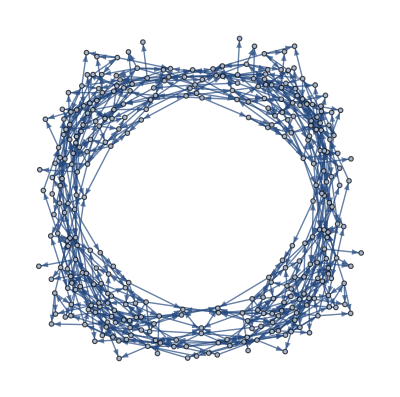

```mathematica
graph=Graph[edges]
```